```mathematica
Grid[{{-Graphics-,"Anno Accademico 2017/18"}},ItemStyle->{Automatic,{1->{FontFamily->"Roboto Condensed",FontSize->20}}},Frame-> True,FrameStyle->{RGBColor[0.94,0.94,0.94]},Alignment->{{Left,Right}},Spacings->10,ItemSize-> Fit]
```

-Graphics- | Anno Accademico 2017/18

```mathematica
Grid[{{"Sistemi Lineari e Metodo di Gauss"}},ItemSize->Fit,Frame->True, FrameStyle->{RGBColor[0.13,0.52,0.96]},Spacings->{5,7},Background->{RGBColor[0.84,0.93,0.98]},ItemStyle->{Automatic, {1-> {FontFamily-> "Roboto Condensed", FontSize->40, FontColor->RGBColor[0.13,0.52,0.96]}}}]
```

Sistemi Lineari e Metodo di Gauss

```mathematica
Grid[{{-Graphics-, Column[{Style["Progetto D'Esame:", Red],"Matematica Computazionale (LM Informatica)\nCalcolo Numerico e Software Didattico (LM Matematica)","Sara Annese\nLaura Cappelli\nMatteo Del Vecchio\nMatteo Marchesini\nDaniele Rossi\nSilvia Scibilia"},Frame->None,Spacings->1]}}, ItemSize->Fit, Frame->None, Alignment->{{Right, Left}},Spacings->3, ItemStyle->{Automatic, {1-> {FontFamily->"Roboto Condensed", FontSize-> 18}}}]
```

-Graphics- | Progetto D'Esame:
Matematica Computazionale (LM Informatica)
Calcolo Numerico e Software Didattico (LM Matematica)
Sara Annese
Laura Cappelli
Matteo Del Vecchio
Matteo Marchesini
Daniele Rossi
Silvia Scibilia

```mathematica
forwardButton = Button[-Graphics-, ImageSize->{80,80}, Appearance->{None}];
Grid[{{forwardButton}},Alignment->{Right}, ItemSize->Fit, Frame->True, FrameStyle->RGBColor[0.94,0.94,0.94], Spacings->{10,3}]
```

```mathematica
{{-Graphics-}}
```

## Ready, Set, Go!

### 1. Clicca sul pulsante in basso per caricare il package necessario

```mathematica
loadPackageButton = Button[Style["Carica Package!", FontSize->30, RGBColor[0.13,0.52,0.96]],
	SetDirectory[NotebookDirectory[]]; Get["GaussLinearSystemsPackage.m"];
	MessageDialog["Il package è stato caricato correttamente!"]
];Grid[{{loadPackageButton}},ItemSize->Fit, Frame->True, FrameStyle->{RGBColor[0.94,0.94,0.94]}, Spacings->{40,0}]
```

Carica Package!

### 2. Valutazione delle celle

Mettere qui foto/gif/video di come fare la valutazione delle celle di inizializzazione

```mathematica
backButton = Button[-Graphics-, Appearance->{None}, ImageSize->{80,80}];
Grid[{{backButton,forwardButton}},Alignment->{{Left, Right}}, ItemSize->Fit, Frame->True, FrameStyle->RGBColor[0.94,0.94,0.94], Spacings->{10,3}]
```

```mathematica
{{-Graphics-, -Graphics-}}
```

## Clicca su un argomento per iniziare...

```mathematica
buttonSistemi = Hyperlink[Button[-Graphics- , Background->White],{"Home.nb", "SistemiLineari"}];
buttonMatrici = Hyperlink[Button[-Graphics-, Background->White], {"Home.nb", "Matrici"}];
buttonGauss = Hyperlink[Button[-Graphics-, Background->White], {"Home.nb", "Gauss"}];
buttonEsercizi = Hyperlink[Button[-Graphics-, Background->White], {"Home.nb", "Esercizi"}];
SetDirectory[NotebookDirectory[]];
blackboard = Import["images/blackboardText.jpg"];
grid = Grid[{{buttonSistemi, buttonMatrici},{buttonGauss, buttonEsercizi}}];
Overlay[{blackboard,grid},All,2,Alignment->Center]
```

```mathematica
-Graphics-{{-Graphics-Home.nbSistemiLineariHome.nb, -Graphics-Home.nbMatriciHome.nb}, {-Graphics-Home.nbGaussHome.nb, -Graphics-Home.nbEserciziHome.nb}}
```

## Dai sistemi lineari...

## Nozioni fondamentali

```mathematica
firstPart = "Un sistema lineare è un sistema costituito da equazioni in cui le ";
styledPart = "incognite";
lastPart = " compaiono al primo grado.";
styledString = {firstPart, Style[styledPart, Red], lastPart};
styledString = Apply[StringJoin, ToString[#, StandardForm] & /@ styledString];
Grid[{{styledString}}, Frame->All, FrameStyle->RGBColor[1.0,0.0,0.0],ItemSize->Scaled[1],Spacings->{2,2},ItemStyle->Directive[FontFamily->"Roboto Condensed", FontSize->24, TextAlignment->Left]]
```

Un sistema lineare è un sistema costituito da equazioni in cui le incognite compaiono al primo grado.

```mathematica
styledString2 = {"Le lettere x,y,z rappresentano le ", Style["incognite", Red], " del sistema. \n I termini a, b, c sono detti ", Style["coefficienti", RGBColor[0.13,0.52,0.96]], " e gli altri elementi sono chiamati ", Style["termini noti", RGBColor[0.14,0.61,0.14]]};
styledString2 = Apply[StringJoin, ToString[#, StandardForm]& /@styledString2];
Grid[{{styledString2}}, Frame -> None, ItemSize->Scaled[1], Spacings->{2, 2},ItemStyle->Directive[FontFamily->"Roboto Condensed", FontSize->24, TextAlignment->Left]]
```

Le lettere x,y,z rappresentano le incognite del sistema. 
 I termini a, b, c sono detti coefficienti e gli altri elementi sono chiamati termini noti

```mathematica
Equations/:MakeBoxes[Equations[eqs_,Alignment->True],TraditionalForm]:=RowBox[{"{",MakeBoxes[#,TraditionalForm]&@Grid[{#1,"=",#2}&@@@{##}&@@eqs,Alignment->{{Right,Center,Left}}]}]

eqExample1= {Style[Subscript[a,1],RGBColor[0.13,0.52,0.96]]x+ Subscript[b,1]y+Subscript[c,1]z == Subscript[d,1], Subscript[a,2]x+ Subscript[b,2]y+Subscript[c,2]z ==  Subscript[d,2],
Subscript[a,3]x+ Subscript[b,3]y+Subscript[c,3]z == Subscript[d,3]};

highlightRules = <|x -> ToString[Style["x",Red], StandardForm],y -> ToString[Style["y",Red], StandardForm], z -> ToString[Style["z",Red], StandardForm],a -> ToString[Style["a",RGBColor[0.13,0.52,0.96]],StandardForm],b -> ToString[Style["b",RGBColor[0.13,0.52,0.96]],StandardForm], c -> ToString[Style["c",RGBColor[0.13,0.52,0.96]],StandardForm], d -> ToString[Style["d",RGBColor[0.14,0.61,0.14]],StandardForm] |>;
eqExample1 = eqExample1 /.highlightRules;

eqExample2 = {Style[7,RGBColor[0.13,0.52,0.96]]x+ Style[6,RGBColor[0.13,0.52,0.96]]y + Style[5,RGBColor[0.13,0.52,0.96]]z ==  Style[5,RGBColor[0.14,0.61,0.14]], Style[3,RGBColor[0.13,0.52,0.96]]x + Style[4,RGBColor[0.13,0.52,0.96]]y + Style[2,RGBColor[0.13,0.52,0.96]]z ==  Style[1,RGBColor[0.14,0.61,0.14]], Style[5,RGBColor[0.13,0.52,0.96]]x + Style[6,RGBColor[0.13,0.52,0.96]]y+Style[4,RGBColor[0.13,0.52,0.96]]z== Style[1,RGBColor[0.14,0.61,0.14]]};
eqExample2 = eqExample2 /. highlightRules;
Grid[{{Equations[eqExample1,Alignment->True]//TraditionalForm,"ESEMPIO\n⟹" ,Equations[eqExample2,Alignment->True]//TraditionalForm}}, Frame->None, ItemSize->Fit, Spacings->{1,1}, ItemStyle->Directive[FontFamily->"Roboto Condensed",FontSize -> 30, TextAlignment->Center]]
```

{a_1 x+b_1 y+c_1 z | = | d_1
a_2 x+b_2 y+c_2 z | = | d_2
a_3 x+b_3 y+c_3 z | = | d_3 | ESEMPIO
⟹ | {7 x+6 y+5 z | = | 5
3 x+4 y+2 z | = | 1
5 x+6 y+4 z | = | 1

#### Attento! Le incognite sono x, y, z, le altre lettere che compaiono sono tutti numeri. Non confonderti!

```mathematica
backButton = Button[-Graphics-, Appearance->{None}, ImageSize->{80,80}];
Grid[{{backButton,forwardButton}},Alignment->{{Left, Right}}, ItemSize->Fit, Frame->True, FrameStyle->RGBColor[0.94,0.94,0.94], Spacings->{10,3}]
```

```mathematica
{{-Graphics-, -Graphics-}}
```

## Dai sistemi lineari...

## I sistemi di equazioni di primo grado: Esempio di un sistema di due equazioni in due incognite

```mathematica
(*eqType1String = "Due equazioni in due incognite";
eqType2String = "Tre equazioni in tre incognite";
eqType3String = {Style["m", Bold], " equazioni in ", Style["n", Bold], " incognite (caso più generale)"};
eqType3String = Apply[StringJoin, ToString[#, StandardForm] & /@ eqType3String];*)

(*rulesIncognite = <|x->Style["x", Red], y->Style["y", Red], z->Style["z", Red]|>;
rulesCoefficienti = <|2->Style["2", RGBColor[0.13,0.52,0.96]],3->Style["3", RGBColor[0.13,0.52,0.96]]|>;
rulesTerminiNoti = <|12->Style["12", RGBColor[0.14,0.61,0.14]],7->Style["7", RGBColor[0.14,0.61,0.14]]|>;
hightlightRules = <|x->Style["x", Red], y->Style["y", Red], z->Style["z", Red]|>;

Equations/:MakeBoxes[Equations[eqs_,Alignment->True],TraditionalForm]:=RowBox[{"{",MakeBoxes[#,TraditionalForm]&@Grid[{#1,"=",#2}&@@@{##}&@@eqs,Alignment->{{Right,Center,Left}}]}]

eqsType1={Subscript[a,1] x + Subscript[b, 1] y == Subscript[c,1],Subscript[a,2] x + Subscript[b, 2] y == Subscript[c,2]};
eqsType1 = eqsType1 /. hightlightRules;

eqsType2 = {Subscript[a,1] x + Subscript[b, 1] y + Subscript[c,1] z == Subscript[d,1],Subscript[a,2] x + Subscript[b, 2] y + Subscript[c,2] z == Subscript[d,2], Subscript[a,3] x + Subscript[b, 3] y + Subscript[c,3] z == Subscript[d,3]};
eqsType2 = eqsType2 /. hightlightRules;

eqsType3 = {Subscript[a, 11] Subscript[x, "1"] + Subscript[a, 12] Subscript[x, "2"] + Subscript[a, HoldForm[1 n]] Subscript[x, "n"] == Subscript[b, 1],Subscript[a, 21] Subscript[x, "1"] + Subscript[a, 22] Subscript[x, "2"] + Subscript[a, HoldForm[2 n]] Subscript[x, "n"] == Subscript[b, 2],Subscript[a, 31] Subscript[x, "1"] + Subscript[a, 32] Subscript[x, "2"] + Subscript[a, HoldForm[3 n]] Subscript[x, "n"] == Subscript[b, 3],Subscript[a, HoldForm["m1"]] Subscript[x, 1] + Subscript[a, HoldForm[m 2]] Subscript[x, 2] + Subscript[a, HoldForm[m n]] Subscript[x, n] == Subscript[b, "m"]};
eqsType3 = eqsType3 /. hightlightRules;

Grid[{{eqType1String, eqType2String, eqType3String},
{Equations[eqsType1, Alignment->True]//TraditionalForm, Equations[eqsType2, Alignment->True]//TraditionalForm, Equations[eqsType3, Alignment->True]//TraditionalForm}},
Frame->All, ItemSize->Fit, Spacings->{2,2}, ItemStyle->{FontFamily->"Roboto Condensed",{1->Directive[FontSize->20,FontName->"Arial"],2->Directive[FontSize->24]}}];*)
```

```mathematica
eqs2x2 = {2x+3y==12, 3x-y== 7};
eqs2x2
plotSolution = Solve[eqs2x2]
eqs2x2Vis = eqs2x2 /. rulesIncognite /. rulesCoefficienti /. rulesTerminiNoti;
Equations[eqs2x2Vis, Alignment ->True] // TraditionalForm
```

{2 x+3 y==12,3 x-y==7}

{{x→3,y→2}}

{2 x+3 y | = | 12
3 x-y | = | 7

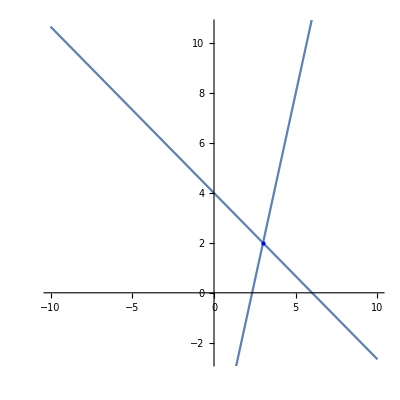
{2 x+3 y | = | 12
3 x-y | = | 7 | -Graphics-
Legenda qua |

```mathematica
Grid[{{Equations[eqs2x2Vis, Alignment->True]//TraditionalForm, plotLinearSystem2[eqs2x2[[1]], eqs2x2[[2]]]}, {"Legenda qua", SpanFromAbove}}, Frame->All,Spacings->{5,5}]
(*plot1 = Plot[y/.Solve[2x+3y==12],{x,0,10}];
plot2 =Plot[y/.Solve[3x-y== 7], {x,0,10}];
g=Graphics[{PointSize[Large],Blue,Point[{3,2}]}];
Show[plot1, plot2,g]*)
```

```mathematica
backButton = Hyperlink[Button[-Graphics-, Appearance->{None}, ImageSize->{80,80}],{"Home.nb", "BlackboardHeader"}];
Grid[{{backButton,forwardButton}},Alignment->{{Left, Right}}, ItemSize->Fit, Frame->True, FrameStyle->RGBColor[0.94,0.94,0.94], Spacings->{10,3}]
```

-Graphics-Home.nbBlackboardHeaderHome.nb | -Graphics-

## Dai sistemi lineari...

## Risoluzione

```mathematica
myString1 = Style["Dovresti già conoscere qualche metodo per risolvere i sistemi lineari, ad esempio:", FontFamily-> "Roboto Condensed", FontSize-> 24];
myString2 = Style["• Metodo di sostituzione o del confronto \n• Metodo di riduzione", FontFamily-> "Roboto Condensed", FontSize-> 20];
Grid[{{myString1},{Framed[myString2,FrameMargins->{{0,350},{0,0}},FrameStyle->None]}}, Frame -> None]

nextChapterButton = Button[Style["prossimo capitolo", FontFamily-> "Roboto Condensed", FontSize-> 24, RGBColor[0.13,0.52,0.96], Bold], Appearance-> {None}];
myString3 = {Style["Prosegui al ",FontFamily-> "Roboto Condensed", FontSize-> 24],nextChapterButton , Style[" per scoprire un nuovo strumento per trovare la soluzione di sistemi lineari.", FontFamily-> "Roboto Condensed", FontSize-> 24]};
myString3 = Apply[StringJoin, ToString[#, StandardForm]& /@ myString3];
Grid[{{myString3}}, Frame -> None]

(*homeButton = Button[-Graphics-, Appearance-> {None},ImageSize-> {80,80}];
Grid[{{Framed[HomeButton,FrameMargins-> {{0,0}, {0, 60}},FrameStyle -> None]}}, Frame -> None]*)
```

Dovresti già conoscere qualche metodo per risolvere i sistemi lineari, ad esempio:
• Metodo di sostituzione o del confronto 
• Metodo di riduzione

Prosegui al prossimo capitolo per scoprire un nuovo strumento per trovare la soluzione di sistemi lineari.